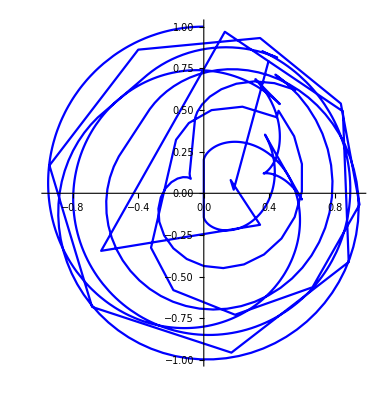

4.71239

5.75959

```mathematica
ClearAll["Global`*"];
getAngle[t_,b_]:=2Pi+Pi/2-2Pi*(t-b^Floor[Log[b,t]])/b^Floor[Log[b,t]];
p1[t_]:={Cos[getAngle[t,2]],Sin[getAngle[t,2]]};
p2[t_]:={Cos[getAngle[t,3]],Sin[getAngle[t,3]]};
(*m[t_]:=Tan[(getAngle[t,2]+getAngle[t,3])/2];*)
m[t_]:=(p2[t][[2]]-p1[t][[2]])/(p2[t][[1]]-p1[t][[1]]);
f[x_,t_]:=m[t](x-p1[t][[1]])+p1[t][[2]];


(*F[x_,y_,t_]:=(y-p1[t][[2]])(p2[t][[1]]-p1[t][[1]])-(x-p1[t][[1]])(p2[t][[2]]-p1[t][[2]]);
Print[FullSimplify[F[x,y,t]]];*)
F[x_,y_,t_]:=x Cos[2^(1-Floor[Log[t]/Log[2]]) π t]-x Cos[2 3^(-Floor[Log[t]/Log[3]]) π t]-y Sin[2^(1-Floor[Log[t]/Log[2]]) π t]+y Sin[2 3^(-Floor[Log[t]/Log[3]]) π t]+Sin[2 (2^(-Floor[Log[t]/Log[2]])-3^(-Floor[Log[t]/Log[3]])) π t];
(*Fd[t_]:=D[F[x_,y_,t],t];
Print[Fd[t]];*)
Fd[x_,y_,t_]:=-Cos[2^(1-Floor[Log[t]/Log[2]]) π t] y (2^(1-Floor[Log[t]/Log[2]]) π-2^(1-Floor[Log[t]/Log[2]]) π (Piecewise[{{0, Log[t]/Log[2]>Floor[Log[t]/Log[2]]}, {Indeterminate, True}}]))+Cos[2 3^(-Floor[Log[t]/Log[3]]) π t] y(2 3^(-Floor[Log[t]/Log[3]]) π-2 3^(-Floor[Log[t]/Log[3]]) π (Piecewise[{{0, Log[t]/Log[3]>Floor[Log[t]/Log[3]]}, {Indeterminate, True}}]))+Cos[2 (2^(-Floor[Log[t]/Log[2]])-3^(-Floor[Log[t]/Log[3]])) π t] (2 (2^(-Floor[Log[t]/Log[2]])-3^(-Floor[Log[t]/Log[3]])) π+2 π t (-(2^(-Floor[Log[t]/Log[2]]) (Piecewise[{{0, Log[t]/Log[2]>Floor[Log[t]/Log[2]]}, {Indeterminate, True}}]))/t+(3^(-Floor[Log[t]/Log[3]]) (Piecewise[{{0, Log[t]/Log[3]>Floor[Log[t]/Log[3]]}, {Indeterminate, True}}]))/t))-x (2^(1-Floor[Log[t]/Log[2]]) π-2^(1-Floor[Log[t]/Log[2]]) π (Piecewise[{{0, Log[t]/Log[2]>Floor[Log[t]/Log[2]]}, {Indeterminate, True}}])) Sin[2^(1-Floor[Log[t]/Log[2]]) π t]+x(2 3^(-Floor[Log[t]/Log[3]]) π-2 3^(-Floor[Log[t]/Log[3]]) π (Piecewise[{{0, Log[t]/Log[3]>Floor[Log[t]/Log[3]]}, {Indeterminate, True}}])) Sin[2 3^(-Floor[Log[t]/Log[3]]) π t];

parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
(*ParametricPlot[parametricFunc[t],{t,0.0001,0.001},PlotStyle->Blue]*)
ParametricPlot[parametricFunc[t],{t,0.001,2},PlotStyle->Blue]
(*Print[FullSimplify[m[t]]];
Print[FullSimplify[x[t]]];
Print[FullSimplify[y[t]]];*)
Print[N[getAngle[3,2]]];
Print[N[getAngle[12,3]]];
(*ParametricPlot[{x[u],y[ u]},{u,1,100}]*)
(*ListPlot[Table[{N[x[u]],N[y[u]]},{u,1,200,2}],Frame->False,Axes->False]*)
```